ⅇ^(-a/x^2)

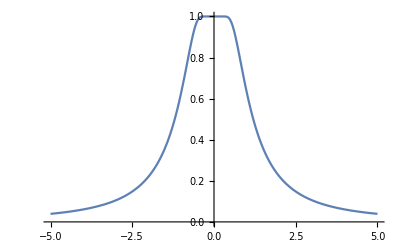

```mathematica
f=Exp[-a/x^2]
Plot[1-f/.a->1,{x,-5,5}]
```

ConditionalExpression[ⅇ^(-5/y^2) y-√(5 π) Erfc[(√5)/y],Re[y]≥0]

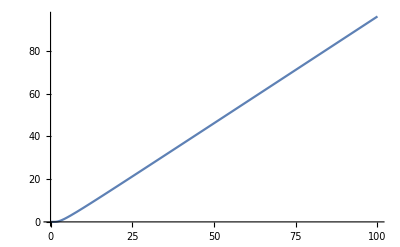

```mathematica
Integrate[f/.a->5,{x,0,y}]
Plot[%,{y,0,100}]
```

```mathematica
Series[f,{x,1,5}]//Normal
%/.a->0/.x->0
```

ⅇ^-a+2 a ⅇ^-a (-1+x)+a (-3+2 a) ⅇ^-a (-1+x)^2+2/3 a (6-9 a+2 a^2) ⅇ^-a (-1+x)^3+1/6 a (-30+75 a-36 a^2+4 a^3) ⅇ^-a (-1+x)^4+1/15 a (90-330 a+255 a^2-60 a^3+4 a^4) ⅇ^-a (-1+x)^5

1

-Graphics-

```mathematica
Integrate[(Q*k+l^2)*DiracDelta[(k+Q)*(l^2+k*Q)-l^2*k],{k,-1,1}]
```

ConditionalExpression[((2 l^2-Q (Q+√(-4 l^2+Q^2))) Boole[-2<Q+√(-4 l^2+Q^2)<2])/(2 Abs[Q √(-4 l^2+Q^2)]),-2<Q+√(-4 l^2+Q^2)<2]

```mathematica
%//FullSimplify
```

ConditionalExpression[(2 l^2-Q (Q+√(-4 l^2+Q^2)))/(2 √(-4 l^2 Q^2+Q^4)),-2<Q+√(-4 l^2+Q^2)<2]

```mathematica
Integrate[Log[m^2/(Q^2*t)],{t,0,t}]
```

ConditionalExpression[t (log(m^2/(Q^2 t))+1),Re(t)>0∧Im(t)==0]

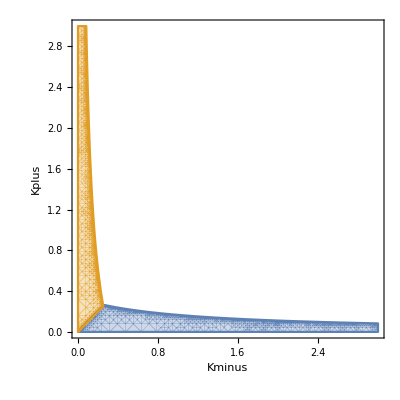

```mathematica
RegionPlot[{km>kp&&tau>(kp+kp*km)/.tau->1/3,kp>km&&tau>(km+kp*km+km^2/4)/.tau->1/3},{km,0,3},{kp,0,3},AxesLabel-> {Kminus,Kplus},MaxRecursion->10]
```

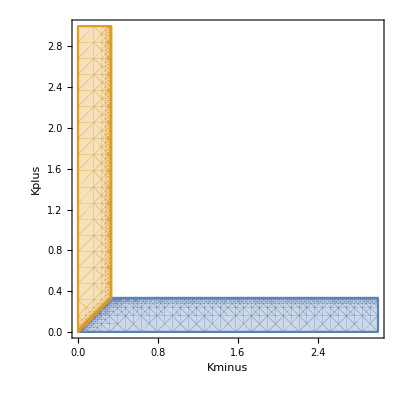

```mathematica
RegionPlot[{km>kp&&tau>kp/.tau->1/3,kp>km&&tau>km/.tau->1/3},{km,0,3},{kp,0,3},AxesLabel-> {Kminus,Kplus},MaxRecursion->10]
```

```mathematica
Sqrt[(1-km-km*kp/(1-km))]
%/.p2->1-kp-km*kp/(1-km)
%/.kp->l^2*kp/.km->l^2*km
Series[%,{l,0,4}]//Normal
%/.l->1
tauhat=1-%*2//FullSimplify
```

√(-(km kp)/(1-km)-km+1)

√(-(km kp)/(1-km)-km+1)

√(-(km kp l^4)/(1-km l^2)-km l^2+1)

l^4 (-km^2/8-(km kp)/2)-(km l^2)/2+1

-km^2/8-(km kp)/2-km/2+1

km^2/4+km kp+km-1

```mathematica
Sqrt[p2^2/4+(km+kp)^2/4+p2*(kp+km)/2-p2*km]
%/.p2->1-kp-km*kp/(1-km)
%/.kp->l^2*kp/.km->l^2*km
Series[%,{l,0,4}]//Normal
%/.l->1
tauhat=1-%*2//FullSimplify
```

√(1/2 p2 (km+kp)+1/4 (km+kp)^2-km p2+p2^2/4)

√(1/4 (km+kp)^2+1/2 (-(km kp)/(1-km)-kp+1) (km+kp)+1/4 (-(km kp)/(1-km)-kp+1)^2-km (-(km kp)/(1-km)-kp+1))

√(1/4 (km l^2+kp l^2)^2-km l^2 (-(km kp l^4)/(1-km l^2)-kp l^2+1)+1/4 (-(km kp l^4)/(1-km l^2)-kp l^2+1)^2+1/2 (km l^2+kp l^2) (-(km kp l^4)/(1-km l^2)-kp l^2+1))

1/2 km kp l^4-(km l^2)/2+1/2

(km kp)/2-km/2+1/2

km-km kp

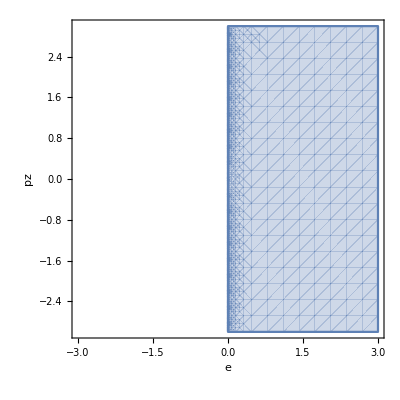

```mathematica
RegionPlot[{e>0},{e,-3,3},{pz,-3,3},AxesLabel-> {e,pz},MaxRecursion->10]
```

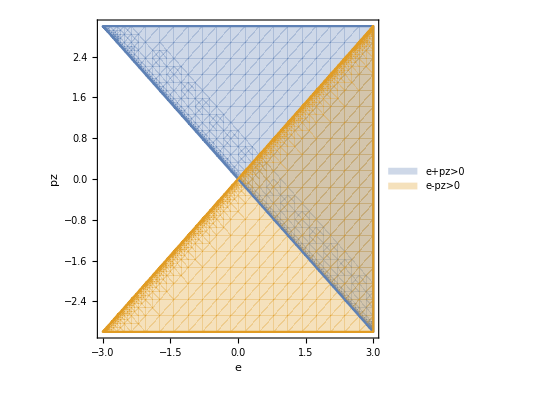

```mathematica
RegionPlot[{e+pz>0,e-pz>0},{e,-3,3},{pz,-3,3},AxesLabel-> {e,pz},MaxRecursion->10,PlotLegends->"Expressions"]
```

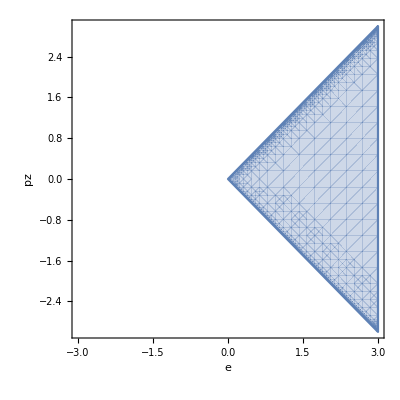

```mathematica
RegionPlot[{e+pz>0&&e-pz>0},{e,-3,3},{pz,-3,3},AxesLabel-> {e,pz},MaxRecursion->10]
```

```mathematica
Gamma[2]
```

1

```mathematica
8*g^2*Cf*HeavisideTheta[t]*(1/(2*eps)-1/(2-2*eps))
%*Pi^(1-eps)*(t)^(-2*eps)/(Gamma[2-2*eps]*(2*Pi)^(3-2*eps))
%*(Exp[EulerGamma]mu^2/( Q^2))^(eps)/Gamma[1+eps]
%/.g^2->8*Pi^2alpha/Cf
Series[%,{eps,0,0}]//Normal
FullSimplify[%,Assumptions->t>0&&Q>0&&mu>0]
Series[%,{eps,0,0}]//Normal
```

8 Cf (1/(2 eps)-1/(2-2 eps)) g^2 t

(Cf 2^(2 eps) (1/(2 eps)-1/(2-2 eps)) π^(eps-2) g^2 t^(-2 eps) t)/(2-2 eps)

(Cf 2^(2 eps) ⅇ^(ℽ eps) (1/(2 eps)-1/(2-2 eps)) π^(eps-2) g^2 t^(-2 eps) t (mu^2/Q^2)^eps)/(2-2 eps eps+1)

(alpha 2^(2 eps+3) ⅇ^(ℽ eps) (1/(2 eps)-1/(2-2 eps)) π^eps t^(-2 eps) t (mu^2/Q^2)^eps)/(2-2 eps eps+1)

(4 alpha t)/eps+4 (alpha t log(mu^2/Q^2)+alpha t-2 alpha t log(t)+alpha log(π) t+2 alpha log(2) t)

(4 alpha (eps log((4 π mu^2)/(Q^2 t^2))+eps+1))/eps

(4 alpha)/eps+4 (alpha log((4 π mu^2)/(Q^2 t^2))+alpha)

```mathematica
Gamma[(D-2)/2]/Pi^((D-2)/2)//FullSimplify
%/.D->4-2*eps//FullSimplify
```

π^(1-D/2) D/2-1

π^(eps-1) 1-eps

```mathematica
(* 
  phase space in Dalitz-space 
-- 
blue is region A, orange is region B, green is region C 
*)
RegionPlot[{2x13+x23<1&&x13+x23<1&&x23>x13&&x13<tau/.tau->1/4,x13+2x23<1&&x13+x23<1&&x13>x23&&x23<tau/.tau->1/4,2x13+x23>1&&x13+2x23>1&&x13+x23<1&&x23+x13>1-tau/.tau->1/4},{x23,0,1},{x13,0,1},AxesLabel-> {x13,x23},MaxRecursion->10]
```

```mathematica
(* 
  phase space in qhatm-qhatp with A region kinematics
-- 
blue is region A, orange is region B, green is region C 
*)
RegionPlot[{(2x13+x23<1&&x13+x23<1&&x23>x13&&x13<tau/.tau->1/4)/.x13->qhatp/(1-qhatm)/.x23->qhatm*(1-qhatm-qhatp)/(1-qhatm),(x13+2x23<1&&x13+x23<1&&x13>x23&&x23<tau/.tau->1/4)/.x13->qhatp/(1-qhatm)/.x23->qhatm*(1-qhatm-qhatp)/(1-qhatm),(2x13+x23>1&&x13+2x23>1&&x13+x23<1&&x23+x13>1-tau/.tau->1/4)/.x13->qhatp/(1-qhatm)/.x23->qhatm*(1-qhatm-qhatp)/(1-qhatm)},{qhatp,0,1},{qhatm,0,1},AxesLabel-> {x13,x23},MaxRecursion->10]
```

-Graphics-

```mathematica
(* 
  phase space in qhatm-qhatp with B region kinematics
-- 
blue is region A, orange is region B, green is region C 
*)
RegionPlot[{(2x13+x23<1&&x13+x23<1&&x23>x13&&x13<tau/.tau->1/10)/.x13->qhatp*(1-qhatm-qhatp)/(1-qhatp)/.x23->qhatm/(1-qhatp),(x13+2x23<1&&x13+x23<1&&x13>x23&&x23<tau/.tau->1/10)/.x13->qhatp*(1-qhatm-qhatp)/(1-qhatp)/.x23->qhatm/(1-qhatp),(2x13+x23>1&&x13+2x23>1&&x13+x23<1&&x23+x13>1-tau/.tau->1/10)/.x13->qhatp*(1-qhatm-qhatp)/(1-qhatp)/.x23->qhatm/(1-qhatp)},{qhatp,0,1},{qhatm,0,1},AxesLabel-> {x13,x23},MaxRecursion->10]
```

-Graphics-

```mathematica
(* 
  phase space in qhatm-qhatp with C region kinematics
-- 
blue is region A, orange is region B, green is region C 
*)
RegionPlot[{(2x13+x23<1&&x13+x23<1&&x23>x13&&x13<tau/.tau->1/4)/.x13->p1hatp*(1-p1hatm-p1hatp)/(1-p1hatp)/.x23->1-p1hatm-p1hatp,(x13+2x23<1&&x13+x23<1&&x13>x23&&x23<tau/.tau->1/4)/.x13->p1hatp*(1-p1hatm-p1hatp)/(1-p1hatp)/.x23->1-p1hatm-p1hatp,(2x13+x23>1&&x13+2x23>1&&x13+x23<1&&x23+x13>1-tau/.tau->1/4)/.x13->p1hatp*(1-p1hatm-p1hatp)/(1-p1hatp)/.x23->1-p1hatm-p1hatp},{p1hatp,0,1},{p1hatm,0,1},AxesLabel-> {x13,x23},MaxRecursion->10]
```

-Graphics-

```mathematica
(* 
  phase space in qhatm-qhatp with A region kinematics
-- 
blue is region A, orange is region B, green is region C 
*)
RegionPlot[{(x13>(1-2*tau)&&(x13+x23)<1/.tau->1/20)/.x13->qhatp/(1-qhatm)/.x23->qhatm*(1-qhatm-qhatp)/(1-qhatm)},{qhatp,0,1},{qhatm,0,1},AxesLabel-> {x13,x23},MaxRecursion->15]
```

-Graphics-

```mathematica
(* 
  phase space in qhatm-qhatp with A region kinematics
-- 
blue is region A, orange is region B, green is region C 
*)
RegionPlot[{(2x13+x23<1&&x23>x13&&x13<tau&&x13>0&&x23>0/.tau->1/10)/.x23->qhatm*(1-x13),(x13+2x23<1&&x13>x23&&x23<tau&&x13>0&&x23>0/.tau->1/10)/.x23->qhatm*(1-x13),(2x13+x23>1&&x13+2x23>1&&x13+x23<1&&x23+x13>1-tau&&x13>0&&x23>0/.tau->1/10)/.x23->qhatm*(1-x13)},{qhatm,0,1},{x13,0,1},AxesLabel-> {x13,x23},MaxRecursion->10]
```

-Graphics-

```mathematica
tautau=0.32
{2x13+x23<1&&x13+x23<1&&x23>x13&&0<x13<tautau,x13+2x23<1&&x13+x23<1&&x13>x23&&0<x23<tautau,2x13+x23>1&&x13+2x23>1&&x13+x23<1&&x23+x13>1-tautau}/.x23->u-v*Cot[Pi/3]/.x13->v*Csc[Pi/3]
%/.u->u/(2/Sqrt[3])/.v->v/(2/Sqrt[3])
(* 
  phase space in symmetric Dalitz-space 
-- 
blue is region A, orange is region B, green is region C 
*)
RegionPlot[%,{u,0,2/Sqrt[3]},{v,0,1},AxesLabel-> {x13,x23},MaxRecursion->10]
```

0.32

{u+√3 v<1∧u+v/(√3)<1∧u-v/(√3)>(2 v)/(√3)∧0<(2 v)/(√3)<0.32,2 (u-v/(√3))+(2 v)/(√3)<1∧u+v/(√3)<1∧(2 v)/(√3)>u-v/(√3)∧0<u-v/(√3)<0.32,u+√3 v>1∧2 (u-v/(√3))+(2 v)/(√3)>1∧u+v/(√3)<1∧u+v/(√3)>0.68}

{(√3 u)/2+(3 v)/2<1∧(√3 u)/2+v/2<1∧(√3 u)/2-v/2>v∧0<v<0.32,2 ((√3 u)/2-v/2)+v<1∧(√3 u)/2+v/2<1∧v>(√3 u)/2-v/2∧0<(√3 u)/2-v/2<0.32,(√3 u)/2+(3 v)/2>1∧2 ((√3 u)/2-v/2)+v>1∧(√3 u)/2+v/2<1∧(√3 u)/2+v/2>0.68}

-Graphics-

```mathematica
N@Sqrt[3]/2
```

0.866025

```mathematica
1/(2*Sqrt[3])//N
%*3
```

0.288675

0.866025

```mathematica
(* 
  phase space in Dalitz-space 
-- 
blue is region A, orange is region B, green is region C 


 ALL THESE a's SHOULD BE REPLACED WITH a/2 
*)
fA[x13_,x23_,a_]:=(x13 (x13+x23-1) (-x23/(x13 (x13+x23-1)))^a-x13 x23 (-(x13+x23-1)/(x13 x23))^a)/(x13-1)
fB[x13_,x23_,a_]:=(x23 (x13+x23-1) (-x13/(x23 (x13+x23-1)))^a-x13 x23 (-(x13+x23-1)/(x13 x23))^a)/(x23-1)
fC[x13_,x23_,a_]:=-((x13+x23-1) (x23 (-x13/(x23 (x13+x23-1)))^a+x13 (-x23/(x13 (x13+x23-1)))^a))/(x13+x23)
tautau=5;
aa=1.1;
RegionPlot[{2x13+x23<1&&x13+x23<1&&x23>x13&&0<fA[x13,x23,aa]<tautau,x13+2x23<1&&x13+x23<1&&x13>x23&&0<fB[x13,x23,aa]<tautau,2x13+x23>1&&x13+2x23>1&&x13+x23<1&&0<fC[x13,x23,aa]<tautau},{x23,0,1},{x13,0,1},AxesLabel-> {x13,x23},MaxRecursion->5]
```

-Graphics-

```mathematica
(* various ways to write the kinemtics using p2perp=0 *)
regAkinQhat[e_]:=e/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p1hatm->1-qhatm/.p2hatp->(1-qhatp/(1-qhatm))/.p1hatp->qhatp*qhatm/(1-qhatm)/.p2hatm->0/.x12->1-x13-x23/.x23->qhatm*(1-x13)/.x13->qhatp/(1-qhatm);
regAkinx1323[e_]:=e/.x12->1-x13-x23/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p1hatm->1-qhatm/.p2hatp->(1-qhatp/(1-qhatm))/.p1hatp->qhatp*qhatm/(1-qhatm)/.p2hatm->0/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13);
```

```mathematica
delta=Pi/3;
epsilon=0.2;

bound0=0<x13+x23<1&&0<x13<1&&0<x23<1//regAkinQhat
anglebound12=ArcCos[1-2x12/(x1*x2)]/.x1->1-x23/.x2->1-x13/.x3->1-x12//regAkinQhat//Simplify
anglebound13=ArcCos[1-2x13/(x1*x3)]/.x1->1-x23/.x2->1-x13/.x3->1-x12//regAkinQhat//Simplify
anglebound23=ArcCos[1-2x23/(x2*x3)]/.x1->1-x23/.x2->1-x13/.x3->1-x12//regAkinQhat//Simplify

energybound1=x1/.x1->1-x23/.x2->1-x13/.x3->1-x12//regAkinQhat//Simplify
energybound2=x2/.x1->1-x23/.x2->1-x13/.x3->1-x12//regAkinQhat//Simplify
energybound3=x3/.x1->1-x23/.x2->1-x13/.x3->1-x12//regAkinQhat//Simplify

RegionPlot[{bound0&&anglebound12<delta,bound0&&anglebound13<delta,bound0&&anglebound23<delta,bound0&&energybound1<2epsilon,bound0&&energybound2<2epsilon,bound0&&energybound3<2epsilon},{qhatm,0,1},{qhatp,0,1},AxesLabel-> {x13,x23},MaxRecursion->10]
```

anglebound[]

0<qhatp/(1-qhatm)+qhatm (1-qhatp/(1-qhatm))<1&&0<qhatp/(1-qhatm)<1&&0<qhatm (1-qhatp/(1-qhatm))<1

ArcCos[(-1-qhatm^2+qhatm (2+qhatp))/(1+qhatm^2+qhatm (-2+qhatp))]

ArcCos[(qhatm^3+2 qhatm^2 (-1+qhatp)+qhatm (-1+qhatp)^2-qhatp)/((1+qhatm^2+qhatm (-2+qhatp)) (qhatm+qhatp))]

ArcCos[(-qhatm+qhatp)/(qhatm+qhatp)]

1-(qhatm (-1+qhatm+qhatp))/(-1+qhatm)

(-1+qhatm+qhatp)/(-1+qhatm)

qhatm+qhatp

-Graphics-

```mathematica
delta=Pi/3;
epsilon=0.2;

bound0=0<x13+x23<1&&0<x13<1&&0<x23<1//regAkinx1323//Simplify
anglebound12=ArcCos[1-2x12/(x1*x2)]/.x12->1-x3/.x1->1-x23/.x2->1-x13/.x3->x13+x23//regAkinx1323//Simplify
anglebound13=ArcCos[1-2x13/(x1*x3)]/.x12->1-x3/.x1->1-x23/.x2->1-x13/.x3->x13+x23//regAkinx1323//Simplify
anglebound23=ArcCos[1-2x23/(x2*x3)]/.x12->1-x3/.x1->1-x23/.x2->1-x13/.x3->x13+x23//regAkinx1323//Simplify

energybound1=x1/.x1->1-x23/.x2->1-x13/.x3->x13+x23//regAkinx1323//Simplify
energybound2=x2/.x1->1-x23/.x2->1-x13/.x3->x13+x23//regAkinx1323//Simplify
energybound3=x3/.x1->1-x23/.x2->1-x13/.x3->x13+x23//regAkinx1323//Simplify

RegionPlot[{bound0&&anglebound12<delta,bound0&&anglebound13<delta,bound0&&anglebound23<delta,bound0&&energybound1<2epsilon,bound0&&energybound2<2epsilon,bound0&&energybound3<2epsilon},{x23,0,1},{x13,0,1},AxesLabel-> {x13,x23},MaxRecursion->15]
```

0<x13+x23<1&&0<x13<1&&0<x23<1

ArcCos[(-1+x13+x23+x13 x23)/((-1+x13) (-1+x23))]

ArcCos[1+(2 x13)/((-1+x23) (x13+x23))]

ArcCos[1+(2 x23)/((-1+x13) (x13+x23))]

1-x23

1-x13

x13+x23